```mathematica
Clear["Global`*"];
ClearSystemCache[];
SetDirectory[NotebookDirectory[]];
```

```mathematica
Install["Suave-Linux"];
Install["Vegas-Linux"];
Install["Divonne-Linux"];
```

## Constants

```mathematica
Clear[mn];
mn=0.939;
G       =  6.67408*^-11; (*Grav Constant*)
vs=230;
vd=270;
cspeed=299792458;
km=1000;
cm=1/100;
Gevto1fm=1000/197.3;
fm1to1m=10^15;
ρχ=0.4;
Prefactor=(1/cm)^3*Gevto1fm*fm1to1m*cspeed//Simplify;
ϵreg=10^(-4);
v=246;
cns=1;(*needs to be fixed*)
```

## Neutron Star EoS

#### Load in data

```mathematica
EoSHeaders = Import["eos_24_lowmass.dat"];
Dataset[EoSHeaders[[1,All]]] (*Print out headings so I know what I'm doing *)
EoSData =Drop[EoSHeaders, 1] ;(* Remove Headings *)
```

Dataset[<>]

Make Interpolating Functions

```mathematica
radius = EoSData[[All,1]];

rMin = radius[[1]];
rMax = Rstar= Last[radius];

μf[x_]     := Interpolation[ EoSData[[All, {1,8}]] ][x*Rstar]*1*^-3; (* Chemical potential in MeV *)

nb          = EoSData[[All,3]];
Yn          = EoSData[[All, 7]];
muList = EoSData[[All, 8]];

ndList = nb*Yn;
nprof[r_] :=Interpolation[ Transpose[{radius,nb*Yn}]][r*Rstar]; (* Neutron density in fm^-1*)

MNS[x_] := Interpolation[EoSData[[All, {1, 2}]]][x*Rstar]*2*^30; (* In units of M_⊙ *) 

p[x_]:=Interpolation[EoSData[[All, {1, 12}]]][x*Rstar];
```

```mathematica
ζ0=5.278368626202642(*Note that is not a problem that it is >1, as I use different units for ntrue and nfree, in same units result is 0.04*);
```

InterpolatingFunction::dmval: Input value {0.00025725} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

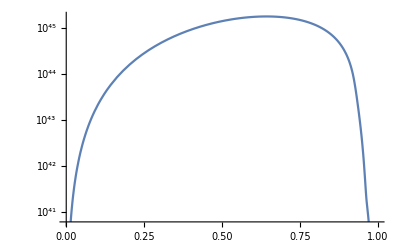

```mathematica
LogPlot[MNS[x]+p[x]*0.1*(x*(Rstar*1*^3))^3, {x, 0, 1}]
```

```mathematica
A[1]
```

A[1]

```mathematica
(1 - (2*G*MNS[1])/(cspeed^2*Rstar*1*^3))*A[1]
```

0.646179 A[1]

```mathematica
b= NDSolveValue[{y'[x]==(2*G*(Rstar*1*^3))/(cspeed^2*(x*(Rstar*1*^3))^2)*(MNS[x]+p[x]*0.1*(x*(Rstar*1*^3))^3/cspeed^2)/(1 - (2*G*MNS[x])/(cspeed^2*(x*(Rstar*1*^3))))*y[x], y[1]==(1 - (2*G*MNS[1])/(cspeed^2*(Rstar*1*^3)))},y, {x, 0, 1}];
(*Plot[y[x]/.sol, {x, 0, 1}]*)
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/0.^2 encountered.

Power::infy: Infinite expression 1/0. encountered.

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NDSolveValue::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {x,y[x]} = {0.,0.435544}.

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

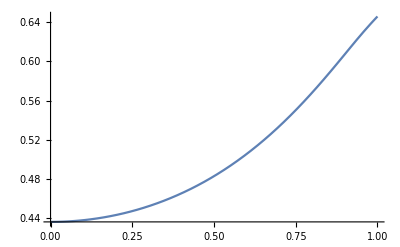
{0.027574,-Graphics-}

```mathematica
Plot[b[x], {x, 0, 1}]//AbsoluteTiming
```